{0,1,2,3,4,5,6,7,8,9,10}

{0,1,2,3,4,5,6,7,8,9,10}

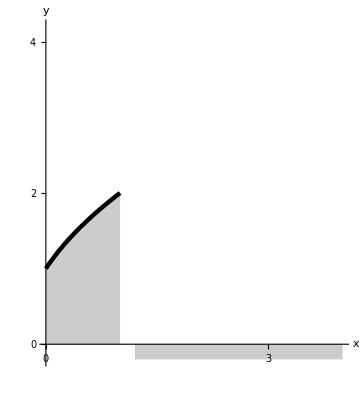

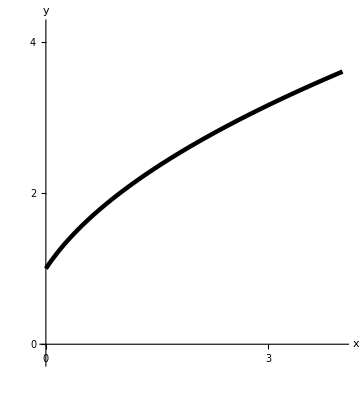

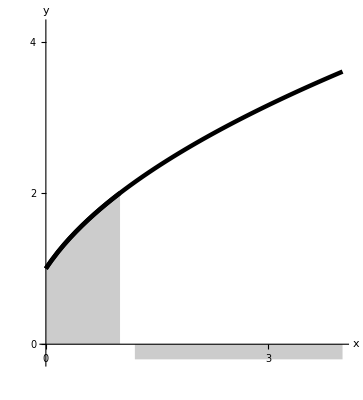

```mathematica
Clear[f,g,x];
f[x_] :=√(1+3x)/;0≤x<1;
f[x_] :=-20/;1.2≤x<4.8;
g[x_] :=√(1+3x)/;0≤x<4;
xTicks=Table[n ,{n,0,10}]
yTicks=Table[n,{n,0,10}]
One=Plot[f[x],{x,0,4},PlotRange->{-0.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Black,Thickness[0.008]}},
AxesLabel->{"x","y"}, AspectRatio-> Automatic, Filling-> Axis]
Onne=Plot[g[x],{x,0,4},PlotRange->{-0.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Black,Thickness[0.008]}},
AxesLabel->{"x","y"}, AspectRatio-> Automatic]
Show[One,Onne]
```

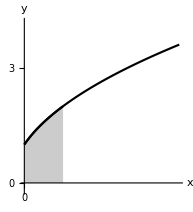
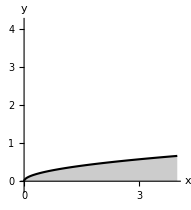
```mathematica
-Graphics--Graphics- -Graphics-
```

{0,1,2,3,4}

{0,1,2,3,4}

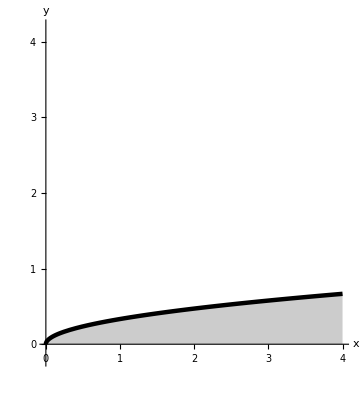

```mathematica
Clear[f,x];
f[x_] :=1/3 √x/;0≤x<4;
f[x_] :=-20/;1.2≤x<4.8;

xTicks=Table[n ,{n,0,4}]
yTicks=Table[n,{n,0,4}]
One=Plot[f[x],{x,0,4},PlotRange->{-0.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Black,Thickness[0.008]}},
AxesLabel->{"x","y"}, AspectRatio-> Automatic, Filling-> Axis]
```

```mathematica
Show[One,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.2]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```

-Graphics-

{0,1,2,3,4,5,6,7,8,9,10}

{0,1,2,3,4,5,6,7,8,9,10}

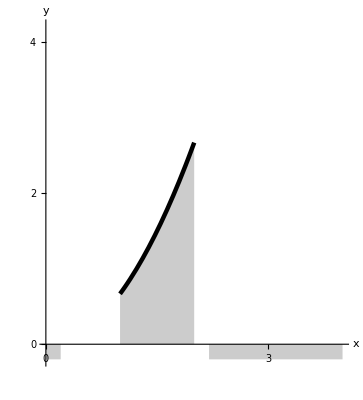

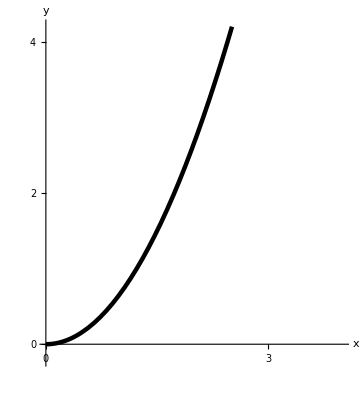

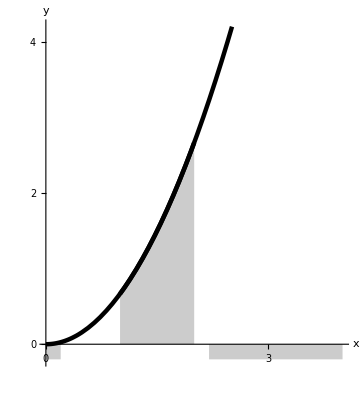

```mathematica
Clear[f,g,x];
f[x_] :=2/3 x^2/;1≤x<2;
f[x_] :=-20/;2.2≤x<4.8;
f[x_] :=-20/;0≤x<0.2;
g[x_] :=2/3 x^2/;0≤x<4;
xTicks=Table[n ,{n,0,10}]
yTicks=Table[n,{n,0,10}]
One=Plot[f[x],{x,0,4},PlotRange->{-0.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Black,Thickness[0.008]}},
AxesLabel->{"x","y"}, AspectRatio-> Automatic, Filling-> Axis]
Onne=Plot[g[x],{x,0,4},PlotRange->{-0.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Black,Thickness[0.008]}},
AxesLabel->{"x","y"}, AspectRatio-> Automatic]
Show[One,Onne]
```

```mathematica
Show[%116,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.175]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```